```mathematica
ClearAll["Global`*"];
```

```mathematica
f[x_,u_,ud_]:=2 u ud;
g[x_,v_,vd_,u_,ud_]:=2(v ud+vd u);
u0=0.5;
uf=1;
s=0.3;
ud0=s;
v0=0;
vd0=1;
phi=1;
x0=0;
xf=1;
```

{0.5,0.584957,0.673023,0.764595,0.860121}

{0.5,0.61721,0.739642,0.86808,1.00344}

{0.5,0.616437,0.738039,0.86558,0.999959}

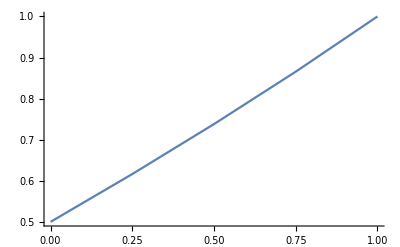

```mathematica
n=4;
h=(xf-x0)/n;
x=Table[j,{j,1,n+1}];
x[[1]]=x0;

u=Table[j,{j,1,n+1}];
ud=Table[j,{j,1,n+1}];
u[[1]]=u0;
ud[[1]]=ud0;

v=Table[j,{j,1,n+1}];
vd=Table[j,{j,1,n+1}];
v[[1]]=v0;
vd[[1]]=vd0;

While[Abs[phi]>0.0005,
For[i=1,i<n+1,i++,
{
k1=(h^2/2)*f[x[[i]],u[[i]],ud[[i]]];
k2=(h^2/2)*f[x[[i]]+(2/3)*h,u[[i]]+(2/3)*h*ud[[i]]+(2/3)*k1,ud[[i]]+(4/3)*h*k1];
u[[i+1]]=u[[i]]+h*ud[[i]]+(1/2)*(k1+k2);
ud[[i+1]]=ud[[i]]+(h/2)*(k1+3*k2);
x[[i+1]]=x[[i]]+h;
}];
phi=u[[n+1]]-uf;
Print[u];
For[i=1,i<n+1,i++,
{
k1=(h^2/2)*g[x[[i]],v[[i]],vd[[i]],u[[i]],ud[[i]]];
k2=(h^2/2)*g[x[[i]]+(2/3)*h,v[[i]]+(2/3)*h*vd[[i]]+(2/3)*k1,vd[[i]]+(4/3)*h*k1,u[[i]],ud[[i]]];
v[[i+1]]=v[[i]]+h*vd[[i]]+(1/2)*(k1+k2);
vd[[i+1]]=vd[[i]]+(h/2)*(k1+3*k2);
x[[i+1]]=x[[i]]+h;
}];
phid=v[[n+1]];
s=s-(phi/phid);
ud[[1]]=s;
]
ListLinePlot[Transpose[{x,u}]]
```

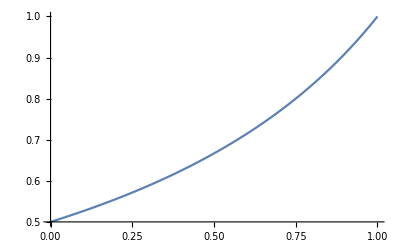

```mathematica
ClearAll["Global`*"];
s=NDSolve[{y''[x]==2*y[x]*y'[x],y[0]==0.5,y[1]==1},y,{x,0,1}];
Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```